# Hamiltonian Evolution for Three Site Rotations

```mathematica
s0 = ({{1, 0}, {0, 1}});
sx = ({{0, 1}, {1, 0}});
sy = ({{0, -ⅈ}, {ⅈ, 0}});
sz=({{1, 0}, {0, -1}});
I0[L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
X[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sx;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Y[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sy;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];

Z[l_,L_]:=Block[{xtp,ltp,i},
ltp = Table[s0,{i,1,L}];
ltp[[l]]=sz;
xtp = ltp[[1]];
For[i=2,i≤L,i++,
xtp=KroneckerProduct[ltp[[i]],xtp];
];

xtp
];
X1 = X[1,3];
Y1 = Y[1,3];
Z1 = Z[1,3];
X2 = X[2,3];
Y2 = Y[2,3];
Z2 = Z[2,3];
X3 = X[3,3];
Y3 = Y[3,3];
Z3 = Z[3,3];
```

## From the initial Hamiltonian

```mathematica
H[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

htp = 1/2 ω1 Z1+1/2 ω2 Z2+1/2 ω3 Z3+Ω1 Cos[ωr1 t +ϕ1] X1+Ω2 Cos[ωr2 t +ϕ2]X2+Ω3 Cos[ωr3 t +ϕ3]X3+1/2 ω12 X1.X2+1/2 ω23 X2.X3+1/2 ω31 X3.X1+Λ X1.X2.X3;

htp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=6;
Λ=0.01;
h=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
U[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ψT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ti,ut,ht,et,ψt},
ψtp=ψ0;
For[ti=dt,ti≤t,ti+=dt,
ut =U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ψtp
];
```

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=6;
Λ=0.01;
dt = 0.01;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt
```

{0.140547+0.284268 ⅈ,-0.024367-0.139851 ⅈ,0.0103932-0.534371 ⅈ,0.0485667-0.0955681 ⅈ,0.304843+0.0434508 ⅈ,-0.0360516-0.0272805 ⅈ,0.305219-0.605713 ⅈ,0.157459-0.0208106 ⅈ}

## After first rotation, before rotating wave approximation

```mathematica
Ha[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

h1=1/2(ω1-ωr1) Z1+Ω1 Cos[ωr1 t +ϕ1]( Cos[t ωr1+ϕ1]I0[3]+ⅈ Sin[t ωr1+ϕ1]Z1).X1;
h2=1/2(ω2-ωr2) Z2+Ω2 Cos[ωr2 t +ϕ2]( Cos[t ωr2+ϕ2]I0[3]+ⅈ Sin[t ωr2+ϕ2]Z2).X2;
h3=1/2(ω3-ωr3) Z3+Ω3 Cos[ωr3 t +ϕ3]( Cos[t ωr3+ϕ3]I0[3]+ⅈ Sin[t ωr3+ϕ3]Z3).X3 ;
h12=1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2);
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3);
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
h123=Λ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3);

htp = h1+h2+h3+h12+h23+h31+h123;

htp
];
```

```mathematica
Ra[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);

ua = (Cos[(ωr1 t+ϕ1)/2]I0[3]-ⅈ Sin[(ωr1 t +ϕ1)/2]Z1).(Cos[(ωr2 t+ϕ2)/2]I0[3]-ⅈ Sin[(ωr2 t +ϕ2)/2]Z2).(Cos[(ωr3 t+ϕ3)/2]I0[3]-ⅈ Sin[(ωr3 t +ϕ3)/2]Z3);


rtp = ua;


rtp
];
```

```mathematica
RdRa[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);

ua =-ⅈ ωr1/2 Z1-ⅈ ωr2/2 Z2-ⅈ ωr3/2 Z3;

rtp = ua;


rtp
];
```

```mathematica
Ua[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Ha[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ψaT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=Conjugate[Transpose[ra]].ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=ra.ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
h=H[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ha=Ha[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
rdr =RdRa[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
```

```mathematica
Max[Abs[ha-Conjugate[Transpose[ra]].h.ra+ⅈ rdr]]
```

7.85046×10^-17

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.001;
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψat = ψaT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
ψt-ψat
```

{-3.55554×10^-9-9.7231×10^-9 ⅈ,2.86012×10^-6-2.06442×10^-6 ⅈ,0.0000493724-0.0000119013 ⅈ,0.0000114699-3.05269×10^-6 ⅈ,0.0000271279-7.26178×10^-6 ⅈ,5.38651×10^-6-2.25348×10^-6 ⅈ,0.0000143117-0.0000168434 ⅈ,2.57411×10^-6-5.30369×10^-6 ⅈ}

## After the rotating wave approximation

```mathematica
Haeff[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];

h1=1/2(ω1-ωr1) Z1+1/2 Ω1 X1;
h2=1/2(ω2-ωr2) Z2+1/2 Ω2 X2;
h3=1/2(ω3-ωr3) Z3+1/2 Ω3 X3 ;
h12=1/2 ω12 ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2);
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]X2- Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3-Sin[t ωr3+ϕ3]Y3);
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3).( Cos[t ωr1+ϕ1]X1-Sin[t ωr1+ϕ1]Y1);
h123=Λ( Cos[t ωr1+ϕ1]X1- Sin[t ωr1+ϕ1]Y1).( Cos[t ωr2+ϕ2]X2-Sin[t ωr2+ϕ2]Y2).( Cos[t ωr3+ϕ3]X3- Sin[t ωr3+ϕ3]Y3);

htp = h1+h2+h3+h12+h23+h31+h123;

htp
];
```

```mathematica
Uaeff[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Haeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
(*ψaeffT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=ra.ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=Conjugate[Transpose[ra]].ψtp;
ψtp
];*)
```

```mathematica
ψaeffT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=Conjugate[Transpose[ra]].ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=ra.ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
(*This part is highly unoptimized*)
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.001;
ovrl={{0,Re[Conjugate[ψ000].ψ000]}};
ovil={{0,Im[Conjugate[ψ000].ψ000]}};
For[t=dt,t≤0.5,t+=dt,
ψt = ψT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
(*ψat = ψaT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];*)
ψaefft = ψaeffT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ov=Conjugate[ψt].ψaefft;
ovrl=Join[ovrl,{{t,Re[ov]}}];
ovil=Join[ovil,{{t,Im[ov]}}];
If[Chop[Mod[t,0.1]]==0,Print[{t,ov}]]
];
```

{0.1,0.999181+0.00138078 ⅈ}

{0.2,0.996711+0.00554386 ⅈ}

{0.3,0.992579+0.0124385 ⅈ}

{0.4,0.986786+0.0219113 ⅈ}

{0.5,0.979347+0.0337167 ⅈ}

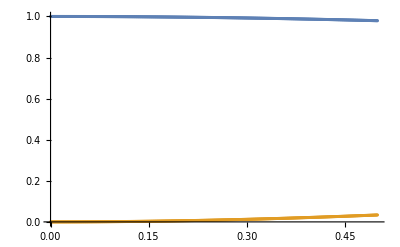

```mathematica
ListPlot[{ovrl,ovil}]
```

## After second rotation

```mathematica
Hc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


h12=1/2 ω12( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2));
h23=1/2 ω23 ( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- (Cos[η2 t]Z2+  Sin[η2 t]Y2)Sin[ζ2] ) - Sin[t ωr2+ϕ2](Cos[η2 t]Y2-Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3));
h31=1/2 ω31 ( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- (Cos[η3 t]Z3+  Sin[η3 t]Y3)Sin[ζ3] ) - Sin[t ωr3+ϕ3](Cos[η3 t]Y3-Sin[η3 t]Z3)).( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- (Cos[η1 t]Z1+  Sin[η1 t]Y1)Sin[ζ1] ) - Sin[t ωr1+ϕ1](Cos[η1 t]Y1-Sin[η1 t]Z1));

h123=Λ ( Cos[t ωr1+ϕ1]( Cos[ζ1]X1- Sin[ζ1]( Cos[η1 t]I0[3].Z1+ Sin[η1 t]Y1))- Sin[t ωr1+ϕ1]( Cos[η1 t]Y1- Sin[η1 t]Z1)).( Cos[t ωr2+ϕ2]( Cos[ζ2]X2- Sin[ζ2]( Cos[η2 t]Z2+Sin[η2 t]Y2))-Sin[t ωr2+ϕ2]( Cos[η2 t]Y2- Sin[η2 t]Z2)).( Cos[t ωr3+ϕ3]( Cos[ζ3]X3- Sin[ζ3]( Cos[η3 t]Z3+ Sin[η3 t]Y3))- Sin[t ωr3+ϕ3]( Cos[η3 t]Y3-Sin[η3 t]Z3));

htp =h12+h23+h31+h123;

htp
];
```

```mathematica
Rc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


uc=(Cos[ζ1/2]I0[3]+ⅈ Sin[ζ1/2]Y1).(Cos[ζ2/2]I0[3]+ⅈ Sin[ζ2/2]Y2).(Cos[ζ3/2]I0[3]+ⅈ Sin[ζ3/2]Y3);

ud=(Cos[η1/2 t]I0[3]-ⅈ Sin[η1/2 t]X1).(Cos[η2/2 t]I0[3]-ⅈ Sin[η2/2 t]X2).(Cos[η3/2 t]I0[3]-ⅈ Sin[η3/2 t]X3);

rtp = uc.ud;


rtp
];
```

```mathematica
RdRc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{rtp,ua,uc,ud,Ω1,ωr1,ϕ1,Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


rtp = -ⅈ 1/2 η1 X1-ⅈ 1/2 η2 X2-ⅈ 1/2 η3 X3;


rtp
];
```

```mathematica
Uc[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Hc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ψcT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψtp,ra,ti,ut,ht,et,ψt},
ra=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0];
ψtp=ψ0;
ψtp=Conjugate[Transpose[ra]].ψtp;
For[ti=dt,ti≤t,ti+=dt,
ut =Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt];
ψtp = ut.ψtp;
];
ra=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
ψtp=ra.ψtp;
ψtp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.4,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;

haeff=Haeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
hc=Hc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];

rc=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
rcc=Conjugate[Transpose[rc]];
rdrc=RdRc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];

Max[Abs[hc-Conjugate[Transpose[rc]].haeff.rc+ⅈ rdrc]]
Max[Abs[rc.hc.rcc +ⅈ rc.rdrc.rcc -haeff]]
```

2.22478×10^-16

1.11239×10^-16

```mathematica
ψ000=Table[0,{i,1,8}];
ψ000[[1]]=1;
dt=0.001;
```

```mathematica
dt=0.001;
ψct=ψ000;
ψaefft=ψ000;
ψct=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0]]].ψct;
For[ti=dt,ti≤t,ti+=dt,
ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψaefft=Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψaefft;
];
ψct=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t].ψct;
```

```mathematica
Max[Abs[ψaefft-ψct]]
```

0.0000114252

```mathematica
ψct = ψcT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
Max[Abs[ψaefft-ψct]]
```

0.0000114252

```mathematica
ψacT[ψ0_,ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{ψct,ra,rc,ti,ut,ht,et,ψt},
ψct=ψ0;
ψct=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0]]].ψct;
ψct=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0]]].ψct;
For[ti=dt,ti≤t,ti+=dt,
ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
];
ψct=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t].ψct;
ψct=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t].ψct;
ψct
];
```

```mathematica
ψaefft = ψaeffT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
ψct = ψacT[ψ000,ωl,ω2l,Λ,Ωl,ωrl,ϕl,t,dt];
```

```mathematica
Max[Abs[ψct-ψaefft ]]
```

0.0000114252

## Averaging over η t

```mathematica
Hη[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


h12=1/4 ω12( Cos[t ωr1+ϕ1+t ωr2+ϕ2]+Cos[t ωr1+ϕ1-t ωr2-ϕ2])Cos[ζ2] Cos[ζ1] ( X1.X2  );
h23=1/4 ω23( Cos[t ωr2+ϕ2+t ωr3+ϕ3]+Cos[t ωr2+ϕ2-t ωr3-ϕ3])Cos[ζ3] Cos[ζ2] ( X2.X3  );
h31=1/4 ω31( Cos[t ωr3+ϕ3+t ωr1+ϕ1]+Cos[t ωr3+ϕ3-t ωr1-ϕ1])Cos[ζ1] Cos[ζ3] ( X3.X1  );

h123=1/4 Λ( Cos[t ωr1+ϕ1+t ωr2+ϕ2+t ωr3+ϕ3]+Cos[t ωr1+ϕ1+t ωr2+ϕ2-t ωr3-ϕ3]+Cos[t ωr1+ϕ1-t ωr2-ϕ2+t ωr3+ϕ3]+Cos[t ωr1+ϕ1-t ωr2-ϕ2-t ωr3-ϕ3])Cos[ζ2] Cos[ζ1]Cos[ζ3] (X3. X1.X2  );

htp =h12+h23+h31+h123;

htp
];
```

```mathematica
Uη[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=Hη[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
dt=0.001;
t=0.5;
ψct=ψ000;
ψηt=ψ000;
ovrl={};
ovil={};
For[ti=dt,ti≤t,ti+=dt,
ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψηt=Uη[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψηt;
ov=Conjugate[ψct].ψηt;
ovrl=Join[ovrl,{{ti,Re[ov]}}];
ovil=Join[ovil,{{ti,Im[ov]}}];
];
```

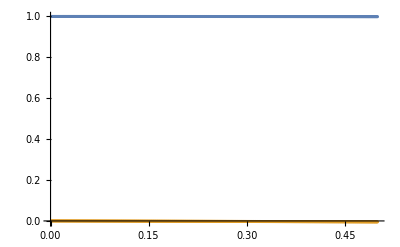

```mathematica
ListPlot[{ovrl,ovil}]
```

## Setting ωr1 = ωr2

```mathematica
H12[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_]:=Block[{htp, h1,h2,h3,h12,h23,h31,h123, Ω1,ωr1,ϕ1, Ω2,ωr2,ϕ2, Ω3,ωr3,ϕ3,ω1,ω2,ω3,ω12,ω23,ω31,ζ1,ζ2,ζ3,η1,η2,η3},
Ω1=Ωl[[1]];  ωr1 = ωrl[[1]];  ϕ1 = ϕl[[1]];
Ω2=Ωl[[2]];    ωr2 = ωrl[[2]];  ϕ2 = ϕl[[2]];
Ω3=Ωl[[3]];    ωr3 = ωrl[[3]];  ϕ3 = ϕl[[3]];
ω1 = ωl[[1]];  ω2 = ωl[[2]];  ω3 = ωl[[3]];
ω12 = ω2l[[1]]; ω23 = ω2l[[2]]; ω31 = ω2l[[3]];
ζ1=ArcTan[(ω1-ωr1)/Ω1];    ζ2=ArcTan[(ω2-ωr2)/Ω2];    ζ3=ArcTan[(ω3-ωr3)/Ω3];  
η1=√((ω1-ωr1)^2+Ω1^2);  η2=√((ω2-ωr2)^2+Ω2^2); η3=√((ω3-ωr3)^2+Ω3^2);


h12=1/4 ω12( Cos[ϕ1-ϕ2])Cos[ζ2] Cos[ζ1] ( X1.X2  );
h23=0;
h31=0;

h123=0;

htp =h12+h23+h31+h123;

htp
];
```

```mathematica
U12[ωl_,ω2l_,Λ_,Ωl_,ωrl_,ϕl_,t_,dt_]:=Block[{utp,ti,ut,ht,et,ψt},
utp=I0[3];
ht=H12[ωl,ω2l,Λ,Ωl,ωrl,ϕl,t];
{et,ψt}=Eigensystem[ht];
utp =Transpose[ψt].DiagonalMatrix[ⅇ^(-ⅈ et dt)].Conjugate[ψt];

utp
];
```

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.6,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.1;
t=500.5;
ψ12t=X1.ψ000;
z1l = {};
z2l={};
z3l={};
For[ti=dt,ti≤t,ti+=dt,
ψ12t=U12[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψ12t;
z1=Conjugate[ψ12t].Z1.ψ12t;
z2=Conjugate[ψ12t].Z2.ψ12t;
z3=Conjugate[ψ12t].Z3.ψ12t;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];
];
```

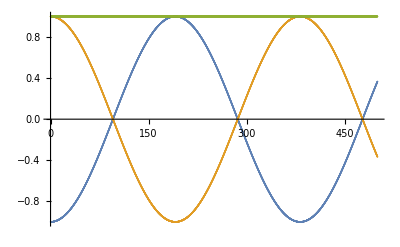

```mathematica
ListPlot[{z1l,z2l,z3l}]
```

### compare to Hη

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={0.04,0.7,0.4};
ωrl={0.6,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.1;
t=500.5;
ψηt=X1.ψ000;
z1l = {};
z2l={};
z3l={};
For[ti=dt,ti≤t,ti+=dt,
ψηt=Uη[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψηt;
z1=Conjugate[ψηt].Z1.ψηt;
z2=Conjugate[ψηt].Z2.ψηt;
z3=Conjugate[ψηt].Z3.ψηt;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];
];
```

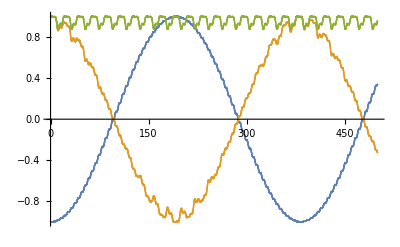

```mathematica
ListPlot[{z1l,z2l,z3l}]
```

### Compare to Hc (note: I had to crank up the drive strengths Ω)

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,2.7,3.4};
ωrl={0.6,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.1;
t=500.5;
ψct=X1.ψ000;
z1l = {};
z2l={};
z3l={};
For[ti=dt,ti≤t,ti+=dt,
ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
z1=Conjugate[ψct].Z1.ψct;
z2=Conjugate[ψct].Z2.ψct;
z3=Conjugate[ψct].Z3.ψct;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];
];
```

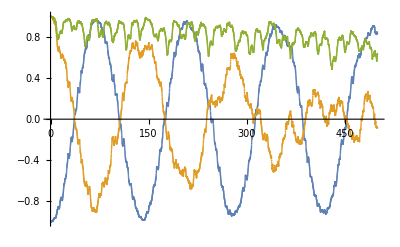

```mathematica
ListPlot[{z1l,z2l,z3l}]
```

### compare to Haeff

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,2.7,3.4};
ωrl={0.6,0.6,0.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.1;
t=500.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψct=X1.ψ000;
ψct=ψct;
For[ti=dt,ti≤t,ti+=dt,
ψt=Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

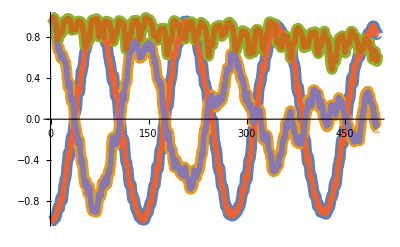

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

### Compare to Ha (I had to adjust the parameters again. The rotating wave approximation is not very accurate).

```mathematica
ωl={0.5,0.4,0.3};
ω2l={0.1,0.15,0.07};
Ωl={1.04,1.04,1.04};
ωrl={6.6,6.6,13.3};
ϕl={0.5,0.9,0.22};
t=0.5;
Λ=0.01;
```

```mathematica
dt=0.01;
t=20.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψct=X1.ψ000;
ψct=ψct;
For[ti=dt,ti≤t,ti+=dt,
ψt=Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];
];
```

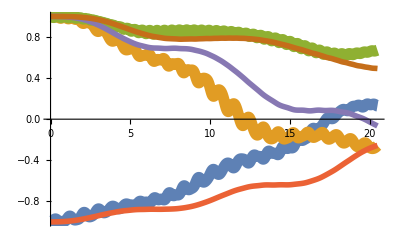

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

### Compare to H

```mathematica
(*New*)
ωl={0.5,0.51,0.49};
ω2l={0.04,0.05,0.07};
Ωl={0.4,0.4,0.001};
ωrl={0.4,0.4,0.4};
ϕl={0.5,0.5,0.5};
t=0.5;
Λ=0.01*0;
```

```mathematica
ωl={0.5,0.51,0.49};
ω2l={0.03,0.04,0.02};
Ωl={0.4,0.4,0.00001};
ωrl={0.4,0.4,10.4};
ϕl={0.5,0.5,0.5};
t=0.5;
Λ=0.01*0;
```

```mathematica
dt=0.2;
t=500.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
z121l={};
z122l={};
z123l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψt=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψt;
ψct=X1.ψ000;
ψ12t=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψot;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];

ψ12t=U12[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψ12t;
ψ12ot=ψ12t;

z121=Conjugate[ψ12ot].Z1.ψ12ot;
z122=Conjugate[ψ12ot].Z2.ψ12ot;
z123=Conjugate[ψ12ot].Z3.ψ12ot;

z121l=Join[z121l,{{ti,z121}}];
z122l=Join[z122l,{{ti,z122}}];
z123l=Join[z123l,{{ti,z123}}];
];
```

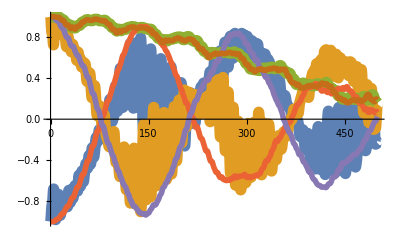

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

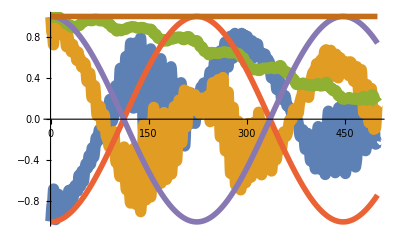

```mathematica
ListPlot[{z1l,z2l,z3l,z121l,z122l,z123l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

### Make sure H and Ha are the same

```mathematica
ωl={0.5,0.51,0.49};
ω2l={0.03,0.04,0.02};
Ωl={0.4,0.4,0.00001};
ωrl={10.4,10.4,10.4};
ϕl={0.5,0.5,0.5};
t=0.5;
Λ=0.01*0;
```

```mathematica
dt=0.1;
t=100.5;
z1l={};
z2l={};
z3l={};
za1l={};
za2l={};
za3l={};
ψt=X1.ψ000;
ψt=ψt;
ψat=X1.ψ000;
ψat=Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0.0].ψat;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψat=Ua[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψat;
ψaot=Conjugate[Transpose[Ra[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψat;

za1=Conjugate[ψaot].Z1.ψaot;
za2=Conjugate[ψaot].Z2.ψaot;
za3=Conjugate[ψaot].Z3.ψaot;

za1l=Join[za1l,{{ti,za1}}];
za2l=Join[za2l,{{ti,za2}}];
za3l=Join[za3l,{{ti,za3}}];
];
```

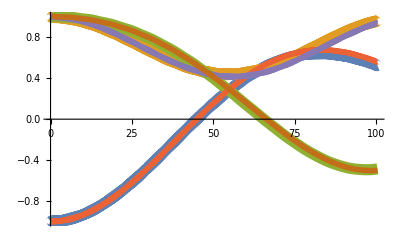

```mathematica
ListPlot[{z1l,z2l,z3l,za1l,za2l,za3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

### Make sure Haeff and Hc are the same

```mathematica
dt=0.2;
t=200;
z1l={};
z2l={};
z3l={};
za1l={};
za2l={};
za3l={};
zc1l={};
zc2l={};
zc3l={};
zη1l = {};
zη2l={};
zη3l={};
ψt=X1.ψ000;
ψt=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψt;
ψat=X1.ψ000;
ψat=Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,0].ψat;
ψct=X1.ψ000;
ψct=ψct;
ψηt=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=Uaeff[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=Conjugate[Transpose[Rc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti]]].ψt;

z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];



ψct=Uc[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψct;
ψcot=ψct;

zc1=Conjugate[ψcot].Z1.ψcot;
zc2=Conjugate[ψcot].Z2.ψcot;
zc3=Conjugate[ψcot].Z3.ψcot;

zc1l=Join[zc1l,{{ti,zc1}}];
zc2l=Join[zc2l,{{ti,zc2}}];
zc3l=Join[zc3l,{{ti,zc3}}];

];
```

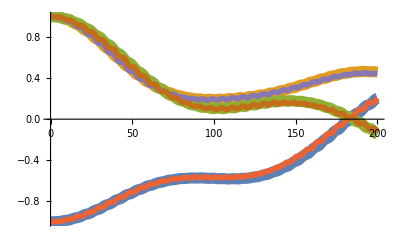

```mathematica
ListPlot[{z1l,z2l,z3l,zc1l,zc2l,zc3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```

### H in the original reference frame

```mathematica
dt=0.01;
t=200.5;
z1l={};
z2l={};
z3l={};
zc1l={};
zc2l={};
zc3l={};
ψt=X1.ψ000;
For[ti=dt,ti≤t,ti+=dt,
ψt=U[ωl,ω2l,Λ,Ωl,ωrl,ϕl,ti,dt].ψt;
ψot=ψt;


z1=Conjugate[ψot].Z1.ψot;
z2=Conjugate[ψot].Z2.ψot;
z3=Conjugate[ψot].Z3.ψot;

z1l=Join[z1l,{{ti,z1}}];
z2l=Join[z2l,{{ti,z2}}];
z3l=Join[z3l,{{ti,z3}}];


];
```

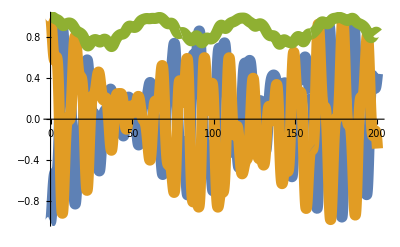

```mathematica
ListPlot[{z1l,z2l,z3l},Joined->True,PlotStyle->{Thickness[0.02],Thickness[0.02],Thickness[0.02],Thickness[0.01],Thickness[0.01],Thickness[0.01]}]
```